#### Born Oppenheimer Approximation

a) Making the BO approximation, write the purely electronic Hamiltonian and, by completing the square,
write its energy levels, E_(el,n)(X).

```mathematica
ϕ[x_]:=(ω/π)^(1/4)Exp[-ω*x^2/2]
Integrate[-ϕ[x] 1/2 D[ϕ[x],{x,2}],{x,-∞,∞},Assumptions->Re[ω]>0]
```

ω/4

```mathematica
Integrate[1/2 ω^2 x^2 ϕ[x]^2,{x,-∞,∞},Assumptions->Re[ω]>0]
```

ω/4

```mathematica
Integrate[-ϕ[x] 1/2 D[ϕ[x],{x,2}],{x,-∞,∞},Assumptions->Re[ω]>0]
```

ω/4

```mathematica
Integrate[1/2 ω^2(x-X)^2 ϕ[x]^2,{x,-∞,∞},Assumptions->Re[ω]>0]
```

1/4 ω (1+2 X^2 ω)

```mathematica
Integrate[x*X*ϕ[x]^2,{x,-∞,∞},Assumptions->Re[ω]>0]
```

0

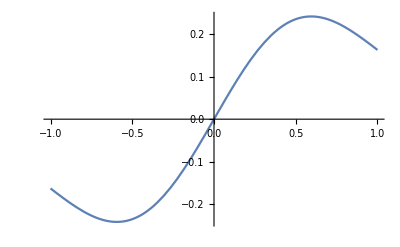

```mathematica
Plot[x*ϕ[x]^2/.ω->Sqrt[2],{x,-1,1}]
```

```mathematica
ϕ2[x_]:=(ω/π)^(1/4)(2ω)^(1/2)x Exp[-ω*x^2/2]
Integrate[-ϕ2[x] 1/2 D[ϕ2[x],{x,2}],{x,-∞,∞},Assumptions->Re[ω]>0]
Integrate[1/2 ω^2(x-X)^2 ϕ2[x]^2,{x,-∞,∞},Assumptions->Re[ω]>0]
Integrate[x*X*ϕ2[x]^2,{x,-∞,∞},Assumptions->Re[ω]>0]
```

(3 ω)/4

1/4 ω (3+2 X^2 ω)

0

b) Write the nuclear equation for the proton in the field of the electronic energy plus any other
parts of the potential, to get an expression for the total energy of the system, E_(ν,n), where ν is the
quantum number for proton vibrations.

```mathematica
ϕnuc[x_]:=((m*ν)/π)^(1/4)Exp[-m*ν*x^2/2]
```

```mathematica
Integrate[-ϕnuc[X] 1/(2*m)D[ϕnuc[X],{X,2}],{X,-∞,∞},Assumptions->{Re[ν]>0,Re[m]>0,Re[m ν]≥0}]
```

ν/4

```mathematica
Integrate[1/2 m*ν^2(x-X)^2 ϕnuc[X]^2,{X,-∞,∞},Assumptions->{Re[ω]>0,Re[m]>0,Re[m ν]≥0}]
```

1/4 ν (1+2 m x^2 ν)

```mathematica
Integrate[x*X*ϕnuc[X]^2,{X,-∞,∞},Assumptions->{Re[ω]>0,Re[m]>0,Re[m ν]≥0}]
```

0

```mathematica
Etot[ν_,n_,m_]:=(1/2+1/2 m x^2 )ν+√2 (n+1/2+2 X^2)
```

c) Assuming m=25, plot the lowest 12 levels, labeling them with their electronic and nuclear quantum
numbers.

```mathematica
Etot[0,0,25]//N
```

1.41421 (0.5+2. X^2)

```mathematica
Table[Etot[1,i,25]/.{x->0,X->0}//N,{i,0,12}]
```

{1.20711,2.62132,4.03553,5.44975,6.86396,8.27817,9.69239,11.1066,12.5208,13.935,15.3492,16.7635,18.1777}

d) The exact solution to this problem is given by the sum of two harmonic oscillators. Show that, if m>>1,
this agrees with your BO solutions above.

```mathematica
exactp[m_]:=1+1/m+Sqrt[1-1/m+1/m^2]
exactm[m_]:=1+1/m-Sqrt[1-1/m+1/m^2]
```

```mathematica
exactp[25]//N
```

2.02061

```mathematica
exactm[25]//N
```

0.0593879